# SHARAQ04 Acceptance

```mathematica
c=299.792458;
mp=938.27205;
mn=939.56538;
md=1875.612858;
mHe4=3727.379;
mB11=10252.548;
mC12=11174.863;
mN13=12111.191;
mN21=19586.63;
mO13=12128.447;
mO14=13044.836;
mO21=19565.350;
mO22=20498.066;
mO23=21434.888;
mO24=22370.840;
mF23=21423.094;
mF24=22358.818;
mF25=23294.025;
massList={mp->"π",mn->"μ",md->"D",mHe4->"α",mB11->"B11",mC12->"C12",mN13->"N13",mN21->"N21",mO13->"O13",mO14->"O14",mO21->"O21",mO22->"O22",mF23-> "F23", mF25->"F25"};
vO={0,0,0};
vX={1,0,0};
vY={0,1,0};
vZ={0,0,1};
```

## Auxiliary functions (must declare)

```mathematica
mE2k[m_,E_]:=√(E^2-m^2);mE2T[m_,E_]:=E-m;
mk2E[m_,k_]:=√(m^2+k^2);mk2T[m_,k_]:=√(m^2+k^2)-m;
mT2E[m_,T_]:=m+T;mT2k[m_,T_]:=√((m+T)^2-m^2);
Ek2m[E_,k_]:=√(E^2-k^2);Ek2T[E_,k_]:=E-√(E^2-k^2);
ET2m[E_,T_]:=E-T;ET2k[E_,T_]:=√(E^2-(E-T)^2);
kT2m[k_,T_]:=(k^2-T^2)/(2 T);kT2E[k_,T_]:=(k^2+T^2)/(2 T);
Momt[V_]:=√(V[[2]]^2+V[[3]]^2+V[[4]]^2);
Mass[V_]:=√(V[[1]]^2-Momt[V]^2)
KE[V_]:=V[[1]]-Mass[V];
Angle[V_]:=If[V[[2]]==0 && V[[3]]==0,{0,0},{ArcTan[V[[4]],√(V[[2]]^2+V[[3]]^2)],If[ArcTan[V[[2]],V[[3]]]<-π/2,ArcTan[V[[2]],V[[3]]]+2π,ArcTan[V[[2]],V[[3]]]]}];
AngleRev[V_]:=If[V[[2]]==0 && V[[3]]==0,{0,0},{ArcTan[-V[[4]],√(V[[2]]^2+V[[3]]^2)],If[ArcTan[V[[2]],V[[3]]]<-π/2,ArcTan[V[[2]],V[[3]]]+2π,ArcTan[V[[2]],V[[3]]]]}];
β[V_]:=Momt[V]/V[[1]];
DisVector[V_,name_]:={name,V[[1]],V[[2]],V[[3]],V[[4]]};
DisEnergy[V_,m_,name_]:={name,V[[1]]-m,Momt[V],Angle[V][[1]] 180/π,Angle[V][[2]] 180/π};
vect[V_]:=Drop[V,{1}];
line[Vstart_,Vend_]:={If[Length[Vstart]==4,vect[Vstart],Vstart],If[Length[Vstart]==4,vect[Vstart],Vstart]+If[Length[Vend]==4,vect[Vend],Vend]};
crossN[V_,U_]:=Join[{0},Cross[vect[V],vect[U]]/(Momt[V] Momt[U])];
Δθ[V_,U_]:=ArcCos[vect[V].vect[U]]/(Momt[V]Momt[U]);
β2γ[β_]:=1/(√(1-β^2));
γ2β[γ_]:=√(1-1/γ^2);
KEA2β[KEA_,A_,m_]:=mT2k[m,KEA A]/mT2E[m,KEA A];
Bρ2KEA[Bρ_,Z_,A_, m_]:=(√(((Bρ Z c)/10^6)^2+m^2)-m)/A;
KEA2Bρ[KEA_,Z_,A_,m_]:=m/(Z c) KEA2β[KEA,A,m] β2γ[KEA2β[KEA,A,m] ] 10^6
```

## Kncockout Kinematics

```mathematica
PmE[m_,E_,θ_,ϕ_]:={E,mE2k[m,E] Sin[θ]Cos[ϕ],mE2k[m,E] Sin[θ]Sin[ϕ],mE2k[m,E] Cos[θ]};
Pmk[m_,k_,θ_,ϕ_]:={mk2E[m,k],k Sin[θ] Cos[ϕ],k Sin[θ]Sin[ϕ],k Cos[θ]};
PmT[m_,T_,θ_,ϕ_]:={m+T,mT2k[m,T]Sin[θ] Cos[ϕ],mT2k[m,T]Sin[θ]Sin[ϕ],mT2k[m,T] Cos[θ]};
PEk[E_,k_,θ_,ϕ_]:={E,k Sin[θ]Cos[ϕ],k Sin[θ]Sin[ϕ],k Cos[θ]};
PET[E_,T_,θ_,ϕ_]:={E,ET2k[E,T] Sin[θ]Cos[ϕ],ET2k[E,T]  Sin[θ]Sin[ϕ],ET2k[E,T]  Cos[θ]};
PkT[k_,T_,θ_,ϕ_]:={kT2E[k,T],k Sin[θ]Cos[ϕ],k Sin[θ]Sin[ϕ],k Cos[θ]};
```

```mathematica
(* basis right-hand rotation operator *)
Rz[θ_]:={{1,0,0,0},{0,Cos[θ],Sin[θ],0},{0,-Sin[θ],Cos[θ],0},{0,0,0,1}};
Ry[θ_]:={{1,0,0,0},{0,Cos[θ],0,-Sin[θ]},{0,0,1,0},{0,Sin[θ],0,Cos[θ]}};
R[α_,θ_,ϕ_]:=Rz[-ϕ].Ry[-θ].Rz[α].Ry[θ].Rz[ϕ];
(* coordinate transform *)
Lz[β_]:={{1/(√(1-β^2)),0,0,β/(√(1-β^2))},{0,1,0,0},{0,0,1,0},{β/(√(1-β^2)),0,0,1/(√(1-β^2))}};
(* title Lorentz operator *)
L[β_,θ_,ϕ_]:= Rz[-ϕ].Ry[-θ].Lz[β].Ry[θ].Rz[ϕ]
```

```mathematica
L[b,θ,0]//MatrixForm
```

(1/(√(1-b^2)) | (b Sin[θ])/(√(1-b^2)) | 0 | (b Cos[θ])/(√(1-b^2))
(b Sin[θ])/(√(1-b^2)) | Cos[θ]^2+Sin[θ]^2/(√(1-b^2)) | 0 | -Cos[θ] Sin[θ]+(Cos[θ] Sin[θ])/(√(1-b^2))
0 | 0 | 1 | 0
(b Cos[θ])/(√(1-b^2)) | -Cos[θ] Sin[θ]+(Cos[θ] Sin[θ])/(√(1-b^2)) | 0 | Cos[θ]^2/(√(1-b^2))+Sin[θ]^2)

```mathematica
Manipulate[Graphics3D[{
{Gray,Line[{{0,0,0},{1,0,0}}]},
Text["x",{1,0,0}],
{Gray,Line[{{0,0,0},{0,1,0}}]},
Text["y",{0,1,0}],
{Gray,Line[{{0,0,0},{0,0,1}}]},
Text["z",{0,0,1}],
{Red,Arrow[{{0,0,0},{Sin[θ]Cos[ϕ],Sin[θ]Sin[ϕ],Cos[θ]}}]},
{Blue,Arrow[{{0,0,0},Evaluate[Drop[{0,Sin[θNN]Cos[ϕNN],Sin[θNN]Sin[ϕNN],Cos[θNN]}.R[α,θ,ϕ],{1}]]}]}
},PlotRange->1,ViewPoint->{15,10,7}],{θ,0,π},{ϕ,0,2π},{θNN,0,π},{ϕNN,0,2π},{α,0,2π}]
```

### Simulation

```mathematica
(* reaction  Normal kinematics A(a,a'+b)B , A = B+b  *)
```

```mathematica
knockout[k_,θk_,ϕk_,θNN_,ϕNN_,S_,mA_,ma_,mb_,TaL_]:={
Pa = PmT[ma,TaL,0,0]; (* incident proton *)
PA=PmT[mA,0,0,0]; (* Target *)
PB=Pmk[mA-mb+S,k,θk,ϕk]; (* residual *)
Pn=PA-PB; (* psudo orbital nucleon *)
PN=If[θk==0,{0,0,1,0},crossN[Pa,Pn]]; (* perpendicular vector of Pa and Pn , default y-axis*)
{θrot,ϕrot}=Angle[PN];
Pc = (Pa+Pn)/2;
βPc = β[Pc];
{θPc,ϕPc}=Angle[Pc];
(* in CM frame *)
Pcc=Pc.L[-βPc,θPc,ϕPc];
Pac=Pa.L[-βPc,θPc,ϕPc];
Pnc=Pn.L[-βPc,θPc,ϕPc];
{θac,ϕac}=Angle[Pac];
Etotal=√(1-βPc^2)(Pa[[1]]+Pn[[1]]); (* total energy of E1c and E2c in CM frame*)
k1c=1/(2 Etotal)(√((Etotal-ma-mb)(Etotal+ma-mb) (Etotal-ma+mb) (Etotal+ma+mb)));
P1c={√(ma^2+k1c^2),k1c Sin[θac]Cos[ϕac],k1c Sin[θac]Sin[ϕac], k1c Cos[θac]}.R[θNN,θrot,ϕrot].R[ϕNN,θac,ϕac];
P2c={√(mb^2+k1c^2) ,k1c Sin[θac]Cos[ϕac],k1c Sin[θac]Sin[ϕac], k1c Cos[θac]}.R[θNN+π,θrot,ϕrot].R[ϕNN,θac,ϕac];
P1=P1c.L[βPc,θPc,ϕPc];
P2=P2c.L[βPc,θPc,ϕPc];
βPa=β[Pa];γPa=γ2β[β[Pa]] ;
PaL=Pa.L[-βPa,0,0];
PAL=PA.L[-βPa,0,0];
PBL=PB.L[-βPa,0,0];
PnL=Pn.L[-βPa,0,0];
P1L=P1.L[-βPa,0,0];
P2L=P2.L[-βPa,0,0];
SepOnline=ma-γPa mb-(γPa  (P1L[[1]]-ma+P2L[[1]]-mb)- βPa γPa (Abs[P1L[[4]]+P2L[[4]]]));
Sep=Mass[PAL+PaL-P1L-P2L]-(mA-mb);
(* output *)
PaL, PAL,P1L,P2L
}
```

```mathematica
size=500;
Manipulate[knockout[k,θk,ϕk,θNN,ϕNN,S,mO14,mp,mp,250];
Graphics3D[{
Black,Text["x",size (1.1)vX], Arrow[line[vO,size vX]],Arrow[line[vO,size vY]],Arrow[line[vO,size vZ]],
Orange,Arrow[Reverse[line[vO,-Pa]]],
Pink,Arrow[line[vO,PB]],
Purple,Arrow[line[vO,Pn]],
Green,Arrow[line[vO,Pc]],
Red,Arrow[line[vO,P1]],
Blue,Arrow[line[vO,P2]],
Blue,Arrow[line[P1,P2]],
Pink,Arrow[line[P1+P2,PB]],
Gray,Arrow[line[vO,P1+P2+PB]],
Black, Text[Sep,-Pa[[2;;4]]]
}]
,{{k,200},0,300},{{θk,π/2},0,2π},{ϕk,0,2π},{{θNN,π/2},0,2π},{{ϕNN,π/6},0,2π},{{S,1},0,2π}]
```

```mathematica
Manipulate[knockout[k,θk °,ϕk °,θNN °,ϕNN °,S,mO,m1,m2,TiL];
TableForm[
{{NumberForm[TableForm[Chop[{
"Setting",{"k",k,"θk, ϕk",θk ,ϕk  },{"S",S,"θNN, ϕNN",θNN ,ϕNN },
{"βPa",βPa},
{"SepOnline", SepOnline},
{"Sep", Sep},
{"Lab frame", "----", "----", "----"},DisVector[PaL,"PaL"],DisVector[PnL,"PnL"],DisVector[P1L,"P1L"],DisVector[P2L,"P2L"],"",
{"", "K.E." , "Momentum", "θ" , "ϕ"},DisEnergy[P1L,m1,"P1L"] ,DisEnergy[P2L,m2,"P2L"],{"β1" , β[P1L]},{"β2" , β[P2L]},(2π-Angle[P1L]-Angle[P2L])180/π,
{"O frame ", "----", "----", "----"},DisVector[Pa,"Pa"],DisVector[Pn,"Pn"],DisEnergy[Pn,m2,""],DisVector[P1,"P1"],DisVector[P2,"P2"],DisVector[P1+P2-Pa-Pn,"Diff"],
{"", "K.E." , "Momentum", "θ" , "ϕ"},DisEnergy[P1,m1,"P1L"] ,DisEnergy[P2,m2,"P2L"],{"β1" , β[P1]},
{"Lorentz", "----", "----", "----"},DisVector[Pc,"Pc"],DisEnergy[Pc,0,""],{"β" , βPc,"γ", 1/(√(1-βPc^2))},DisVector[Pcc,"pcc"],
{"CM frame", "----", "----", "----"},DisVector[Pac,"Pac"],DisVector[Pnc,"Pnc"],DisVector[P1c,"k1c"],DisVector[P2c,"P2c"]
}],TableAlignments->{Right}],6],
Graphics[{
{Black,Arrow[{{-PAL[[2]],-PAL[[4]]},{0,0}}]},
{Pink, Arrow[{{0,0},{PBL[[2]],PBL[[4]]}}]},
{Blue,Arrow[{{0,0},{P1L[[2]],P1L[[4]]}}]},
{Red,Arrow[{{0,0},{P2L[[2]],P2L[[4]]}}]},
{Orange,Arrow[{{-PnL[[2]],-PnL[[4]]},{0,0}}]}
},PlotRange->800,Frame->True,GridLines->Automatic,GridLinesStyle->Directive[Gray,Dotted],PlotLabel-> "Lab, S="<>ToString[S]<>", k="<>ToString[k]<>", θ_k="<>ToString[θk ]<>"°, θ_NN="<>ToString[θNN ]<>"°, ΣT="<>ToString[DisEnergy[P2L,m2,""][[2]]+DisEnergy[P1L,m1,""][[2]]],Epilog->{Text["θ1L="<>ToString[180-Angle[P1L][[1]] 180/π]<>"\nβ1="<>ToString[β[P1L]]<>"\nT1="<>ToString[DisEnergy[P1L,m1,""][[2]]],{P1L[[2]],P1L[[4]]-90}],Text["θ2L="<>ToString[180-Angle[P2L][[1]] 180/π]<>"\nβ2="<>ToString[β[P2L]]<>"\nT2="<>ToString[DisEnergy[P2L,m2,""][[2]]],{P2L[[2]],P2L[[4]]-90}],
Text["Nucleus",{Pa[[2]]+150,Pa[[4]]-100}],
Text["Orbital Neutron",{-PnL[[2]]-200,-PnL[[4]]-50}],
Text["ΔAngle="<>ToString[Δθ[P1L,P2L] 180/π],{0,-620}]},ImageSize->400],
{Graphics[{
{Purple,Arrow[{{-Pa[[2]],-Pa[[4]]},{0,0}}]},
{Pink, Arrow[{{0,0},{PB[[2]],PB[[4]]}}]},
{Blue,Arrow[{{0,0},{P1[[2]],P1[[4]]}}]},
{Red,Arrow[{{0,0},{P2[[2]],P2[[4]]}}]},
{Green,Arrow[{{0,0},{Pc[[2]],Pc[[4]]}}]},
{Orange,Arrow[{{-Pn[[2]],-Pn[[4]]},{0,0}}]}
},PlotRange->800,Frame->True,GridLines->Automatic,GridLinesStyle->Directive[Gray,Dotted],PlotLabel-> "Nucleus",ImageSize->250]
,
Graphics[{{Purple,Arrow[{{-Pac[[2]],-Pac[[4]]},{0,0}}]},
{Blue,Arrow[{{0,0},{P1c[[2]],P1c[[4]]}}]},
{Red,Arrow[{{0,0},{P2c[[2]],P2c[[4]]}}]},
{Orange,Arrow[{{-Pnc[[2]],-Pnc[[4]]},{0,0}}]}
},PlotRange->800,Frame->True,GridLines->Automatic,GridLinesStyle->Directive[Gray,Dotted],PlotLabel-> "C.Momemtum",
Epilog->{Text["T_tot="<>ToString[DisEnergy[Pac,mp,""][[2]]+DisEnergy[Pnc,mn,""][[2]]],{0,500}]},ImageSize->250]
}
}
}]
,{{m1,mp},{mp->"Proton",mn->"Neutron"}},{{m2,mp},{mp->"Proton",mn->"Neutron",mHe4->"alpha"}},{{mO,mF23},massList},{{TiL,245.4},0,300},{{k,10},{0,10,50,100,150,200,270}},{{θk,90},-180,180},{{ϕk,0},-180,180},{{S,0},0,30},{{θNN,90},-180,180},{{ϕNN,0},-180,360},ControlPlacement->Top]
```

## Detectors Resolution

### Detectors Geometry

```mathematica
z0Tpla=1400;z0=1022.37;
FL[V_]:=(2 z0Tpla)/(√3 Abs[Cos[AngleRev[V][[2]]]]Sin[AngleRev[V][[1]]]+Cos[AngleRev[V][[1]]])
ToF[V_]:=FL[V]/(β[V]c)
Sp[Ua_,UA_,V1_,V2_]:=Mass[Ua+UA-V1-V2]-Mass[UA]+Mass[V2]
f[x_]:=Piecewise[{{3/2(x+170),200 2/3-170>x>-170},{200,200 (-2/3)+950>x>200 2/3-170},{-3/2(x-950),950>x>200 (-2/3)+950}},0]
MWDCPosLab[V_]:=z0/z0Tpla FL[V]{Cos[AngleRev[V][[2]]]Sin[AngleRev[V][[1]]],Sin[AngleRev[V][[2]]]Sin[AngleRev[V][[1]]],Cos[AngleRev[V][[1]]]}
MWDCPos[V_]:=RotationMatrix[π/3,{0,If[Abs[AngleRev[V][[2]]]>π/2,1,-1],0}].MWDCPosLab[V]
βbyFLTof[fl_,tof_]:=fl/(tof c);
γbyFLTof[fl_,tof_]:=(tof c)/(√(c^2 tof^2-fl^2));
γβbyFLTof[fl_,tof_]:=fl/(√(c^2 tof^2-fl^2));
New4Vector[V_,Δtof_,Δx_,Δy_]:=Module[{newMWDCPos, newFL},
newMWDCPos=MWDCPos[V]+{Δx,Δy,0};
newFL=z0Tpla/z0 Norm[newMWDCPos];
Mass[V] Join[{γbyFLTof[newFL,ToF[V]+Δtof]},γβbyFLTof[newFL,ToF[V]+Δtof]Normalize[RotationMatrix[π/3,{0,If[Abs[AngleRev[V][[2]]]>π/2,-1,1],0}].newMWDCPos]{1,1,-1}]
]
```

## Monto Carlo Simulation

```mathematica
(* Get the k, θk, ϕk, θNN, ϕNN, Sp  that can be detected*)
```

```mathematica
n=10000;
TKEA=276.7;
kList=Table[RandomReal[{0,200}],{i,1,n}];
(*SpList=Table[RandomChoice[{4.627}(*+{0,3.5,9.54,11.74}*)],{i,1,n}];*)
(*SpList=Table[RandomChoice[{0,5,10,15}],{i,1,n}];*)
(*SpList =Table[RandomChoice[13.26+{0, 3.199,4.582, 4.909}],{i,1,n}];(* 23F *) *)
SpList=Table[RandomChoice[14.43+{0, 4.79,5.37, 7.6}],{i,1,n}];(* 25F *)
θkList=Table[ArcCos[2RandomReal[{0,1}]-1],{i,1,n}];
ϕkList=Table[ π RandomReal[{-1,1}],{i,1,n}];
θNNList=Table[ArcCos[2RandomReal[{0,1}]-1],{i,1,n}];
ϕNNList=Table[π RandomReal[{-1,1}],{i,1,n}];
reactList=Table[knockout[kList[[i]],θkList[[i]],ϕkList[[i]],θNNList[[i]],ϕNNList[[i]],SpList[[i]],mF25,mp,mp,TKEA],{i,1,n}];
```

```mathematica
(* Rearrange List by Left and Right *)
ArrgList = Table[If[reactList[[k,3]][[2]]<0,

 temp = reactList[[k,3]];
 reactList[[k,3]]=reactList[[k,4]];
reactList[[k,4]]=temp;reactList[[k]]
,reactList[[k]]],{k,1, n}];
```

```mathematica
(* Filter List for detector acceptance*)
FiltedList = DeleteCases[Table[
If[f[(MWDCPos[ArrgList[[i,4]]])[[1]]]>Abs[(MWDCPos[ArrgList[[i,4]]])[[2]]], ArrgList[[i]],0],{i,1,n}],0];
m = Length[FiltedList]
```

1512

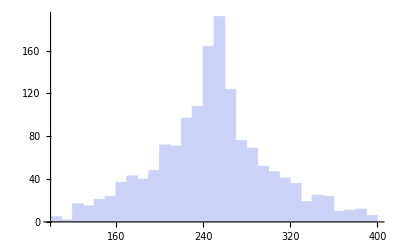

```mathematica
Etot=Table[KE[FiltedList[[i,3]]]+KE[FiltedList[[i,4]]],{i,1,m}];
Histogram[Etot,{100,400,10}]
```

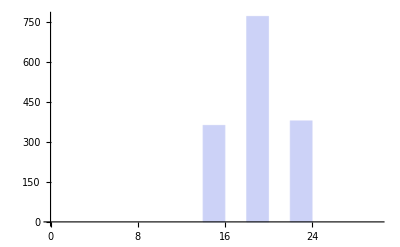

```mathematica
SpF=Table[Sp[FiltedList[[i,1]],FiltedList[[i,2]],FiltedList[[i,3]],FiltedList[[i,4]]],{i,1,m}];
Histogram[SpF,{0,30,2}]
```

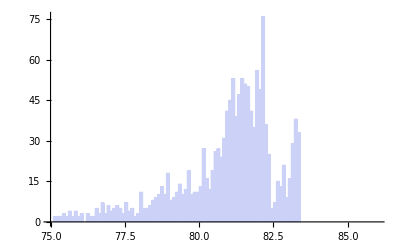

```mathematica
OpAngF=Table[(AngleRev[FiltedList[[i,3]]][[1]]+AngleRev[FiltedList[[i,4]]][[1]])180/π,{i,1,m}];
Histogram[OpAngF,{75,86,0.1}]
```

```mathematica
Δtof1=RandomVariate[NormalDistribution[0,0.3],m];
Δx1=RandomVariate[NormalDistribution[0,0.5],m];
Δy1=RandomVariate[NormalDistribution[0,1.5],m];
Δtof2=RandomVariate[NormalDistribution[0,0.3],m];
Δx2=RandomVariate[NormalDistribution[0,0.5],m];
Δy2=RandomVariate[NormalDistribution[0,1.5],m];
```

```mathematica
MeasureList=Table[{
FiltedList[[i,1]],
FiltedList[[i,2]],
New4Vector[FiltedList[[i,3]],Δtof1[[i]],Δx1[[i]],Δy1[[i]]],
New4Vector[FiltedList[[i,4]],Δtof2[[i]],Δx2[[i]],Δy2[[i]]]
},{i,1,m}];
```

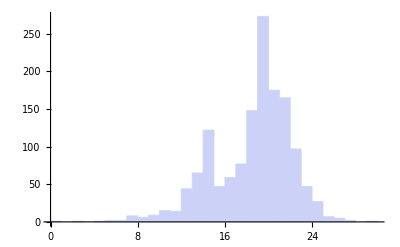

```mathematica
SpM=Table[Sp[MeasureList[[i,1]],MeasureList[[i,2]],MeasureList[[i,3]],MeasureList[[i,4]]],{i,1,m}];
Histogram[SpM,{0,30,1}]
```

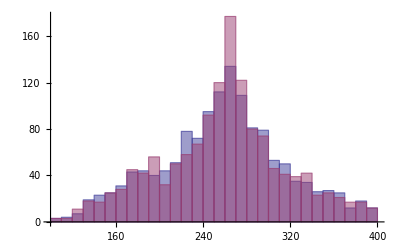

```mathematica
EtotM=Table[KE[MeasureList[[i,3]]]+KE[MeasureList[[i,4]]],{i,1,m}];
Histogram[{EtotM,Etot},{100,400,10}]
```

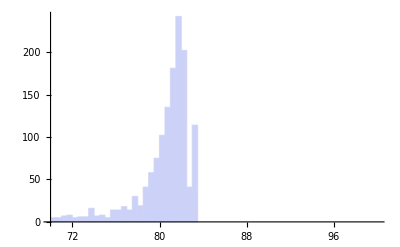

```mathematica
OpAng=Table[(AngleRev[MeasureList[[i,3]]][[1]]+AngleRev[MeasureList[[i,4]]][[1]])180/π,{i,1,m}];
Histogram[OpAng,{70,100,0.5}]
```

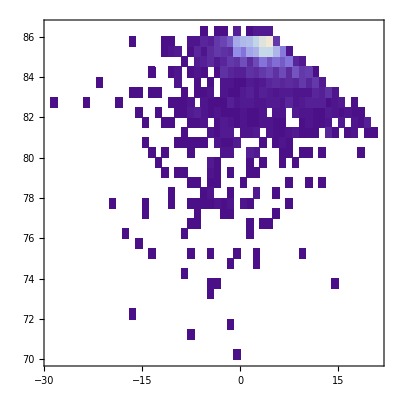

```mathematica
OpAngSp=Table[{SpM[[i]],OpAng[[i]]},{i,1,m}];
DensityHistogram[OpAngSp,{{-30,30,1},{70,100,0.5}}]
```

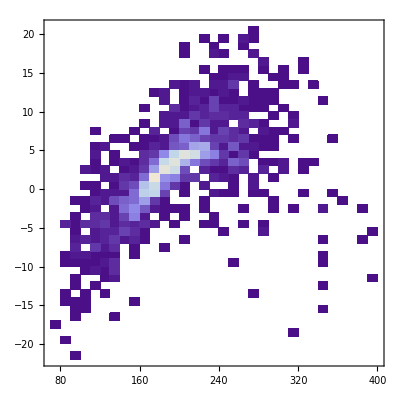

```mathematica
SpEtot=Table[{EtotM[[i]],SpM[[i]]},{i,1,m}];
DensityHistogram[SpEtot,{{0,400,10},{-30,60,1}}]
```